```mathematica
(* VBP1 (Tryps) PREVALENCE *)
```

```mathematica
(* Turn off Solve warning messages *)
Off[Solve::ratnz]

(* Function to generate table of mean burdens for ρ=0 and ρ=1, for all θ1 and θ2 combinations *)
provchange[pars_]:=
Module[{data},
data= Table[Table[Solve[system//.provpars//.pars,{prevv,prevh,nh,nv}][[5]],{prov,0,1}],{θ1,0,5},{θ2,0,5}];
Table[(prevh/.data[[i]][[j]][[2]])-(prevh/.data[[i]][[j]][[1]]),{i,1,6},{j,1,6}]
]

(* Provisioning response calculations *)
provpars={δp->δmin+(δmax-δmin)*E^(-θ1*prov),αp->αmax-(αmax-αmin)*E^(-θ2*prov)};

(* System equations *)
system={αp*ω*prevh*nh*(1-prevv)-bv*prevv*(kv-nv)/kv==0 && αp*δp*prevv*nv*(1-prevh)-(μh+ν+γ)*prevh-prevh*bh*(K-nh)/K+μh*prevh+ν*prevh^2==0 && bh*nh*(K-nh)/K-μh*nh-ν*prevh*nh==0&& bv*nv*(kv-nv)/kv-μv*nv==0};
```

```mathematica
(* GENERATE PLOTS VARYING BY K *)

(* Compile parameter lists *)
pars1={K->42.12,bh->1.24,δ->1,α-> 0.001,γ-> 0.644,ν->0,δmax->0.1056,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->54.7,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars2={K->42.12*1.5,bh->1.24,δ->1,α-> 0.001,γ-> 0.644,ν->0,δmax->0.1056,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->54.7,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars3={K->42.12*2,bh->1.24,δ->1,α-> 0.001,γ-> 0.644,ν->0,δmax->0.1056,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->54.7,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.0623141,0.0826257,0.0898183,0.0924288,0.0933844},{-0.0324711,0.015306,0.0311131,0.0367485,0.038799,0.0395503},{-0.045014,-0.00334256,0.0104905,0.0154329,0.0172328,0.0178925},{-0.0497136,-0.0104023,0.00265541,0.00732406,0.00902476,0.00964821},{-0.0514542,-0.0130273,-0.000261794,0.00430346,0.00596667,0.00657639},{-0.0520962,-0.0139968,-0.00133975,0.00318709,0.00483637,0.005441}}

{{0.,0.0788439,0.104012,0.112844,0.116038,0.117206},{-0.0442609,0.017665,0.038013,0.0452279,0.0478475,0.0488066},{-0.0617261,-0.00735769,0.0106954,0.0171228,0.0194599,0.0203161},{-0.0683242,-0.0169459,0.00017745,0.00628305,0.00850441,0.00931831},{-0.0707756,-0.0205274,-0.00375853,0.00222399,0.00440101,0.00519874},{-0.0716807,-0.0218524,-0.00521568,0.000720896,0.00288137,0.00367305}}

{{0.,0.0914524,0.119908,0.129802,0.133369,0.134672},{-0.0539526,0.0199322,0.0437986,0.0522032,0.055247,0.0563603},{-0.0756636,-0.0101178,0.0113714,0.0189787,0.021739,0.0227493},{-0.0839289,-0.0217588,-0.00126301,0.00600719,0.00864706,0.0096136},{-0.0870087,-0.0261252,-0.00601262,0.00112702,0.00372019,0.00466972},{-0.0881471,-0.0277432,-0.00777399,-0.000683304,0.00189234,0.0028355}}

-0.1

0.2

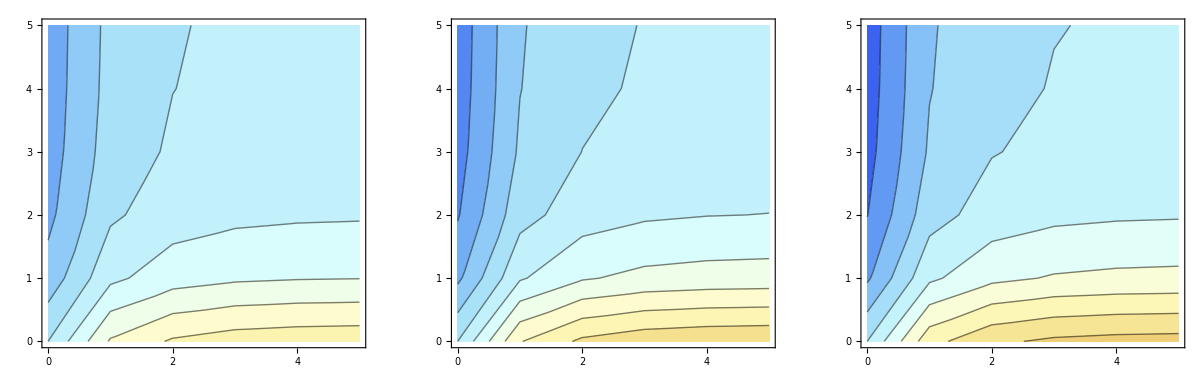

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY b *)

(* Compile parameter lists *)
pars1={K->42.12,bh->1.24,δ->1,α-> 0.001,γ-> 0.644,ν->0,δmax->0.1056,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->54.7,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars2={K->42.12,bh->1.24*1.5,δ->1,α-> 0.001,γ-> 0.644,ν->0,δmax->0.1056,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->54.7,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars3={K->42.12,bh->1.24*2,δ->1,α-> 0.001,γ-> 0.644,ν->0,δmax->0.1056,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->54.7,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.0623141,0.0826257,0.0898183,0.0924288,0.0933844},{-0.0324711,0.015306,0.0311131,0.0367485,0.038799,0.0395503},{-0.045014,-0.00334256,0.0104905,0.0154329,0.0172328,0.0178925},{-0.0497136,-0.0104023,0.00265541,0.00732406,0.00902476,0.00964821},{-0.0514542,-0.0130273,-0.000261794,0.00430346,0.00596667,0.00657639},{-0.0520962,-0.0139968,-0.00133975,0.00318709,0.00483637,0.005441}}

{{0.,0.062225,0.0825192,0.0897065,0.0923151,0.0932701},{-0.0324636,0.0152236,0.0310131,0.036643,0.0386916,0.0394423},{-0.0450036,-0.00342234,0.010393,0.01533,0.017128,0.017787},{-0.049702,-0.0104811,0.00255891,0.0072221,0.00892092,0.00954369},{-0.0514423,-0.0131057,-0.000357938,0.00420186,0.00586319,0.00647223},{-0.0520841,-0.0140751,-0.00143576,0.00308563,0.00473302,0.00533697}}

{{0.,0.0621817,0.0824675,0.0896522,0.09226,0.0932147},{-0.0324599,0.0151836,0.0309646,0.0365919,0.0386396,0.0393899},{-0.0449985,-0.00346103,0.0103458,0.01528,0.0170771,0.0177359},{-0.0496964,-0.0105193,0.00251211,0.00717266,0.00887057,0.009493},{-0.0514365,-0.0131437,-0.000404558,0.0041526,0.00581301,0.00642172},{-0.0520782,-0.014113,-0.00148232,0.00303643,0.00468291,0.00528652}}

-0.1

0.1

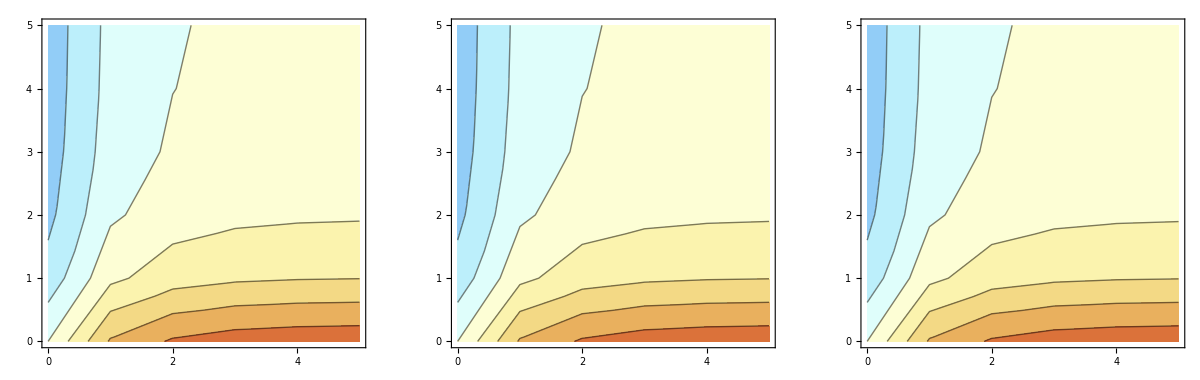

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY μ *)

(* Compile parameter lists *)
pars1={K->42.12,bh->1.24,δ->1,α-> 0.001,γ-> 0.644,ν->0,δmax->0.1056,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->54.7,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars2={K->42.12,bh->1.24,δ->1,α-> 0.001,γ-> 0.644,ν->0,δmax->0.1056,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->54.7,bv->100,kv->K*2,ν->0,μh ->1/13.75/1.5, μv->1/4};
pars3={K->42.12,bh->1.24,δ->1,α-> 0.001,γ-> 0.644,ν->0,δmax->0.1056,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->54.7,bv->100,kv->K*2,ν->0,μh ->1/13.75/2, μv->1/4};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.0623141,0.0826257,0.0898183,0.0924288,0.0933844},{-0.0324711,0.015306,0.0311131,0.0367485,0.038799,0.0395503},{-0.045014,-0.00334256,0.0104905,0.0154329,0.0172328,0.0178925},{-0.0497136,-0.0104023,0.00265541,0.00732406,0.00902476,0.00964821},{-0.0514542,-0.0130273,-0.000261794,0.00430346,0.00596667,0.00657639},{-0.0520962,-0.0139968,-0.00133975,0.00318709,0.00483637,0.005441}}

{{0.,0.0636683,0.0843937,0.0917281,0.0943894,0.0953636},{-0.0333798,0.0155108,0.0316839,0.0374477,0.0395447,0.040313},{-0.0462937,-0.00363719,0.0105292,0.0155897,0.0174325,0.0181079},{-0.0511351,-0.0108925,0.00248398,0.00726607,0.00900799,0.00964652},{-0.0529287,-0.0135911,-0.000512561,0.00416425,0.005868,0.00649258},{-0.0535903,-0.0145879,-0.00161999,0.0030177,0.00470727,0.00532665}}

{{0.,0.0643731,0.0853123,0.0927198,0.0954073,0.096391},{-0.0338534,0.0156203,0.0319838,0.0378145,0.0399356,0.0407127},{-0.0469612,-0.00378748,0.0105529,0.015675,0.0175401,0.0182238},{-0.0518769,-0.0111446,0.00239843,0.00723971,0.00900312,0.00964953},{-0.0536983,-0.0138816,-0.000639401,0.00409564,0.00582055,0.00645287},{-0.0543701,-0.0148926,-0.00176217,0.00293339,0.00464399,0.00527107}}

-0.1

0.1

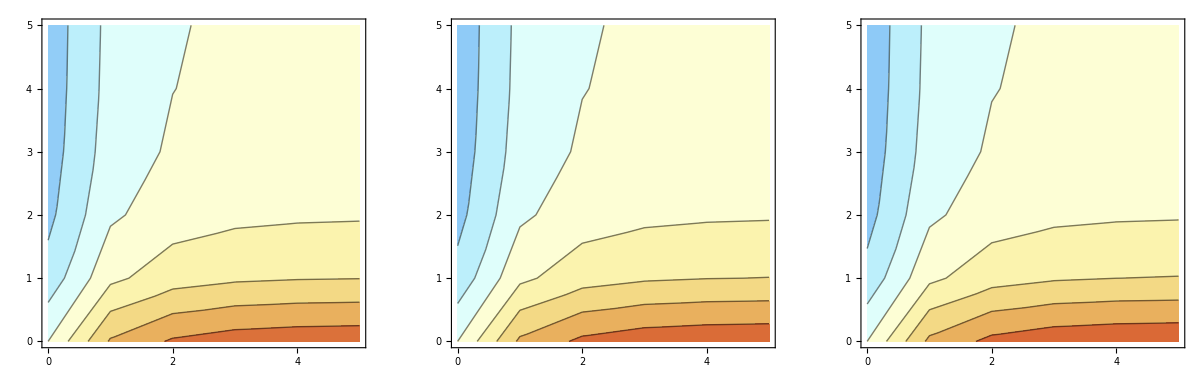

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```